Post (μ:13.4286)

Post (δ:0.0760811)

Post (σ:3.62545)

0.110039 ⅇ^(-0.0380406 (-13.4286+x)^2)

1/2 Erfc[0.19504 (13.4286-x)]

ConditionalExpression[13.4286-5.12716 InverseErfc[2 x],0≤x≤1]

13.4286

0.5

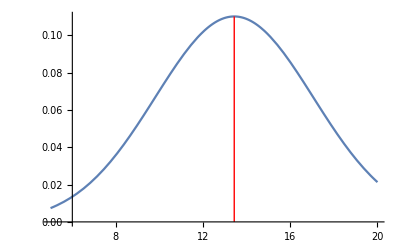

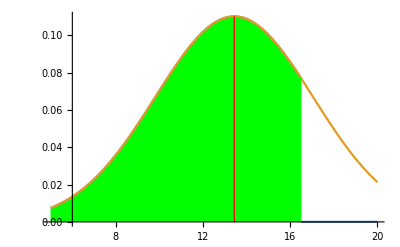

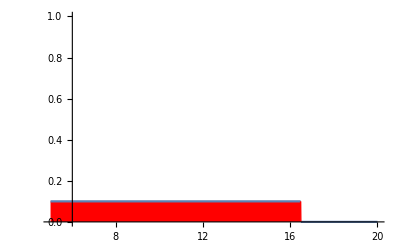

{-∞,16.4798}

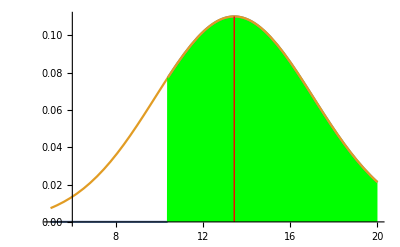

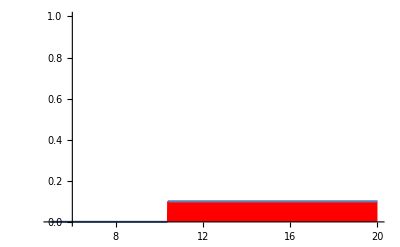

{10.3773,∞}

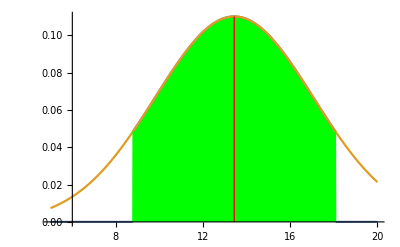

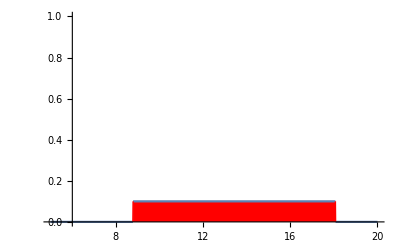

{8.7824,18.0748}

```mathematica
(*Prior for Normal fordeling*)
μpre := 14;
σpre := 6;
δpre := 1/(σpre)^2;
(*Observasjonsdata, hvor n er antall målinger*)
snitt := 13.1;
n := 4;
σdata := 9.1;
δdata :=  n/(σdata)^2;
(*Posterior*)
δpost := δpre+δdata;
μpost := δpre/δpost*μpre+δdata/δpost*snitt;
σpost := 1/Sqrt[δpost];


(*Velg intervall størrelser for grafen*)
Nedre := 5;
Ovre := 20;
(*Velg størrelsen på konfidensintervallet*)
konfint := 0.8;


Post μ:μpost
Post δ:δpost
Post σ:σpost


Temp:=NormalDistribution[μpost,σpost];
f[t_]:=PDF[Temp,t];
F[t_]:=CDF[Temp,t];
Ff[t_]:=InverseCDF[Temp,t];
theInterval[t_,start_,end_]:=UnitStep[t-Ff[start]] (1-UnitStep[t-Ff[1-end]])
cF[t_,start_,end_]:=f[t] theInterval[t,start,end];
ciPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,Nedre,Ovre},PlotRange->All,Filling->{1->{Axis,{Green}},2->{{1},{White}}}]
ciIPlot[start_,end_,range_]:=Plot[0.1 theInterval[x,start,end],{x,Nedre,Ovre},PlotRange->{0,1},Filling->{1->{Axis,{Red}}}]
cendPlot[start_,end_,range_]:=Plot[{cF[x,start,end],f[x]},{x,Nedre,Ovre},PlotRange->All,Filling->{1->{Axis,{White}},2->{{1},{Red}}}]
f[x]
F[x]
Ff[x]
Mean[Temp]
F[Mean[Temp]]//N
Show[Plot[f[t],{t,Nedre,Ovre}],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]]

(*Venstre intervall*)

Show[
ciPlot[0,0.2,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0,0.2,0.03]
{Ff[0.0],Ff[konfint]}

(*Høyre intervall*)
Show[
ciPlot[0.2,0,0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[0.2,0,0.03]
{Ff[1-konfint],Ff[1]}

(*Symetriskkonfidensintervall om μ*)
Show[
ciPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03],DiscretePlot[f[Mean[Temp]],{k,{Mean[Temp]}},FillingStyle->RGBColor[3,0,0,1],PlotStyle->RGBColor[3,0,0,0]]
]
ciIPlot[F[Mean[Temp]]-0.4,0.6-F[Mean[Temp]],0.03]
{Ff[F[Mean[Temp]]-konfint/2],Ff[F[Mean[Temp]]+konfint/2]}
```